# Convert Chemical Line Structure Diagram to Graph Representation

Corwin Kerr

Matthew Szudzik

Github repository: https://github.com/kerrcb/wss19-ck

## Load the Images

I downloaded the 5719 example images and .mol files from the OSRA (Optical Structure Recognition Application, from the NIH) project to enable verification of the determined structure. The file can be downloaded from here: https://cactus.nci.nih.gov/osra/uspto-validation-updated.zip.

```mathematica
validationRoot="path/to/uspto-validation-updated";
validationImages="images";
validationResult="molfiles";
validationDumps="dumps";
```

```mathematica
imFilePaths=FileNames[All,FileNameJoin[{validationRoot,validationImages}]];
```

```mathematica
images=Import[#]&/@imFilePaths;
```

Optional: create a dump file of the images for quick re-importing. Note that the resulting file is about 1.8 GB.

```mathematica
Export[FileNameJoin[{validationRoot,validationDumps,"images.mx"}],images]
```

Export::nodir: Directory /Users/Corwin/path/to/uspto-validation-updated/dumps/ does not exist.

Export::noopen: Cannot open path/to/uspto-validation-updated/dumps/images.mx.

$Failed

To re-import the saved images.

```mathematica
images=Import[FileNameJoin[{validationRoot,validationDumps,"images.mx"}]];
```

Import::nffil: File path/to/uspto-validation-updated/dumps/images.mx not found during Import.

## Load the Package

I am developing the package ChemicalLines to store my necessary functions. For convenience, the entire package is included here, copied July 9, 2019 at 4PM.

```mathematica
BeginPackage["ChemicalRead`"]
```

ChemicalRead`

### Usage Messages

Package

```mathematica
ChemicalRead::usage="ChemicalRead is a package for scanning chemical structures."
```

ChemicalRead is a package for scanning chemical structures.

Line Operations

```mathematica
listPointsSlope::usage="";
lineSlope::usage="";
lineDistance::usage="";
doLineDetect::usage="";
pickLongLines::usage="";
doLongLineDetect::usage="";
lineIntersectQ::usage="";
lineToPointDelta::usage="";
lineAngle::usage="";
```

Visualization

```mathematica
visualizeLineDetect::usage="";
showLines::usage="";
visualizeLongLineDetect::usage="";
```

Line Grouping

```mathematica
gatherParallelLines::usage="";
flattenLines::usage="";
gatherNearbyLinesByCenter::usage="";
gatherIntersectingLines::usage="";
mergeLines::usage="";
```

Vertices

```mathematica
findVertices::usage="";
traceConnections::usage="";
```

Text Recognition

```mathematica
testTextRecognize::usage="";
```

### Begin the private context

```mathematica
Begin["`Private`"]
```

ChemicalRead`Private`

### Definition of the exported functions

#### Line Utilities

```mathematica
(*Unprotect[listPointsSlope]*)
Clear[listPointsSlope]

listPointsSlope[p_?MatrixQ]:=
Quiet[(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])&/@Partition[N[p],2,1],{Power::infy,Infinity::indet}]
```

We sort the points so the angle is taken consistently

```mathematica
Clear[lineAngle]

lineAngle[Line[p_?MatrixQ]]:=
Block[{ps},
ps=Sort[p];
ArcTan[ps[[2,1]]-ps[[1,1]],ps[[2,2]]-ps[[1,2]]]
]
```

```mathematica
Clear[lineSlope]

lineSlope[Line[points_?MatrixQ]]:=listPointsSlope[Sort[points]]
lineSlope[Line[list_/;VectorQ[list,MatrixQ]]]:=lineSlope@*Line/@list
lineSlope[lines__:{__Line}]:=lineSlope/@lines
```

```mathematica
Clear[lineDistance]

lineDistance[Line[points_?MatrixQ]]:=Total[EuclideanDistance@@@Partition[N[points],2,1]]
lineDistance[Line[list_/;VectorQ[list,MatrixQ]]]:=lineDistance@*Line/@list
lineDistance[lines:{__Line}]:=lineDistance/@lines
```

To use Matthew's function

```mathematica
Clear[lineToPointDelta]
lineToPointDelta[l:Line[_?MatrixQ]]:={#,l[[1,2]]-#}&[l[[1,1]]]
lineToPointDelta[l:{Repeated[Line[_?MatrixQ],{1,Infinity}]}]:=lineToPointDelta/@l
```

From Matthew Szudzik

```mathematica
Clear[lineIntersectQ]
lineIntersectQ[a:{Repeated[_?NumericQ,2]},b:{Repeated[_?NumericQ,2]},u:{Repeated[_?NumericQ,2]},v:{Repeated[_?NumericQ,2]}]:=Quiet[Reduce[Exists[{s,t},a+s*b==u+t*v&&0<=s<=1&&0<=t<=1]],Reduce::ratnz]
lineIntersectQ[a:Line[_?MatrixQ],b:Line[_?MatrixQ]]:=Apply[lineIntersectQ,Catenate[Map[lineToPointDelta,{a,b}]]]
lineIntersectQ[{a:Line[_?MatrixQ],b:Line[_?MatrixQ]}]:=lineIntersectQ[a,b]
```

#### Line Grouping

```mathematica
Clear[flattenLines]

flattenLines[Line[list_/;VectorQ[list,MatrixQ]]]:=Line/@list
flattenLines[x:{__Line}]:=flattenLines/@x
(*For already list of flat lines*)
flattenLines[x:{Repeated[Line[_?MatrixQ],{1,Infinity}]}]:=x
(*flattenLines[List[x___Line]]:=flattenLines*)
```

```mathematica
Clear[gatherParallelLines]
(*Only works on line segments*)
(*I won't make it automatically flatten lines because that's a different function.*)

gatherParallelLines[x:{Repeated[Line[_?MatrixQ],{1,Infinity}]},tol_?NumericQ]:=
Block[{combo,grouped},
combo=Transpose[{x,Flatten@*lineSlope@x}/.Indeterminate->99999999999999];
grouped=Gather[combo,Abs[#2[[2]]-#1[[2]]]<tol&];
Return[Transpose[#][[1]]&/@grouped]
]

(*default tolerance*)
gatherParallelLines[x:{Repeated[Line[_?MatrixQ],{1,Infinity}]}]:=gatherParallelLines[x,0.01];
```

Gather lines by proximity. Takes a list of lines

```mathematica
Clear[gatherNearbyLinesByCenter]
gatherNearbyLinesByCenter[lines:{Repeated[Line[_?MatrixQ],{1,Infinity}]},tol_?NumericQ]:=
Gather[lines,EuclideanDistance[Mean[First[#1]],Mean[First[#2]]]<tol&]

gatherNearbyLinesByCenter[lines:{Repeated[Line[_?MatrixQ],{1,Infinity}]}]:=gatherNearbyLinesByCenter[lines,10]
```

Gather lines by intersecting. If the lines are not intersecting, it puts them in their own separate lists.

```mathematica
Clear[gatherIntersectingLines]
gatherIntersectingLines[{line:Line[_?MatrixQ]}]:={{{line}}}

gatherIntersectingLines[lines:{Repeated[Line[_?MatrixQ],{2,Infinity}]}]:=
Block[{s2,s3,s5,s6,s7,s8,s9,s3Group,notIntersecting},
s2=Subsets[lines,{2}];
(*s3=Apply[lineIntersectQ,s2,{1}];*)

s3Group=GroupBy[s2,lineIntersectQ];
If[
KeyExistsQ[s3Group,False]
,notIntersecting=Complement[Flatten@s3Group[False],Flatten@Lookup[s3Group,True,{}]];
,notIntersecting={};
];

(*s5=Transpose[{s2,s3}];
s6=Select[s5,#[[2]]&];
s7=Transpose[s6][[1]];*)
(*s7=Pick[s2,s3];*);

s7=Lookup[s3Group,True,{}];

s8=Gather[s7,IntersectingQ[Part[#1],Part[#2]]&];

If[Dimensions[s8]=={0}
,s9={Map[{#}&,notIntersecting]};
,s9=Join[s8,{Map[{#}&,notIntersecting]},2];
];

Return[s9]
]
```

```mathematica
Clear[mergeLines]
mergeLines[lines:{Repeated[Line[_?MatrixQ],{2,Infinity}]}]:=
Block[{pts,subs,bigLine},
pts=Flatten[First/@lines,1];
subs=Subsets[pts,{2}];
bigLine=MaximalBy[subs,Apply[EuclideanDistance]];
Return[Apply[Line,bigLine]];
]

mergeLines[{line:Line[_?MatrixQ]}]:={line}

(*for the format of gathered intersecting lines*)
mergeLines[l:{Repeated[{Repeated[Line[_?MatrixQ],{2,Infinity}]},{1,Infinity}]}]:=mergeLines[Union[Flatten[l]]]
```

#### Find vertices

```mathematica
Clear[findVertices]

findVertices[lines:{Repeated[Line[_?MatrixQ],{2,Infinity}]},tol_?NumericQ]:=
Mean/@Select[Gather[Flatten[First/@lines,1],EuclideanDistance[#1,#2]<tol&],Length[#]>=2&]

findVertices[lines:{Repeated[Line[_?MatrixQ],{2,Infinity}]}]:=findVertices[lines,3]
```

Gather lines by combination of similar slope and nearby centers along the direction of the ?

#### Trace vertices

```mathematica
Clear[traceConnections]

traceConnections[p_Point,lineGroup:{Repeated[Line[_?MatrixQ],{2,Infinity}]},pointGroup:{Repeated[_Point,{1,Infinity}]},mergedParents_Association,vertexChildren_Association]:=
Block[{pQP,pointIndex,otherPointIndex,otherPoints,otherMergedPoint,connectingIndices},
pQP=mergedParents[p];
pointIndex=Map[Position[lineGroup,#]&,pQP[[;;,1]]];
otherPointIndex=Map[ReplacePart[#,{1,-1}->Mod[#,2]+1&@#[[1,-1]]]&,pointIndex,1];
otherPoints=Flatten@Map[Point@Part[lineGroup,Sequence@@Flatten@#]&,otherPointIndex,{2}];
otherMergedPoint=vertexChildren/@otherPoints;
connectingIndices=Position[pointGroup,#]&/@Flatten@otherMergedPoint;
Return[Flatten@connectingIndices]
]
```

#### Line Detection

```mathematica
Clear[doLineDetect]
doLineDetect[image_Image,tVal_,dVal_]:=
Block[{lines},
lines=ImageLines[ColorNegate[image],tVal,dVal,Method->{"Segmented"->True}];
Return[lines]
]
```

```mathematica
Clear[pickLongLines]
pickLongLines[lines_,lCutoff_]:=Select[Flatten@flattenLines@lines,lineDistance[#]>=lCutoff&]
```

```mathematica
Clear[doLongLineDetect]

doLongLineDetect[image_Image,tVal_,dVal_,lCutoff_]:=
Block[{lines,longLines},
lines=doLineDetect[image,tVal,dVal];
longLines=pickLongLines[lines,lCutoff];

Return[longLines]
]
```

#### Text Recognize

```mathematica
Clear[testTextRecognize]
testTextRecognize[image_,level_,options___]:=
Module[{res},
res=TextRecognize[image,level,options,"BoundingBox"];
HighlightImage[image,{"Boundary",res}]
]
```

#### Shortcut Display Images

```mathematica
Clear[showLines]
showLines[image_Image,lines_:{__Line}]:=HighlightImage[image,{RandomColor[],#}&/@lines]
```

#### Specific Visualization to find parameters

```mathematica
Clear[visualizeLineDetect]
visualizeLineDetect[image_,tVals_,dVals_]:=
With[{i=ColorNegate[image]}
,TableForm[Table[
HighlightImage[image,{Red,ImageLines[i,t,d,Method->{"Segmented"->True}]}],{t,#1},{d,#2}],TableDirections->Row,TableHeadings->{"t = "<>ToString[#]&/@#1,"d="<>ToString[#]&/@#2}]]&[tVals,dVals]
visualizeLineDetect[image_,tVals_,dVals_]:=visualizeLineDetect[image,{tVals},{dVals}]
```

```mathematica
Clear[visualizeLongLineDetect]
visualizeLongLineDetect[image_Image,tVals_List,dVals_List,lCutoff_]:=
Block[{longLines},
TableForm[
Table[
longLines=doLongLineDetect[image,t,d,lCutoff];
HighlightImage[image,{RandomColor[],#}&/@longLines],{t,#1},{d,#2}]
,TableDirections->Row
,TableHeadings->{"t = "<>ToString[#]&/@#1,"d="<>ToString[#]&/@#2}
]
]&[tVals,dVals];
visualizeLongLineDetect[image_Image,tVal_List,dVal_?NumericQ,lCutoff_?NumericQ]:=
visualizeLongLineDetect[image,tVal,{dVal},lCutoff]
visualizeLongLineDetect[image_Image,tVal_?NumericQ,dVal_List,lCutoff_?NumericQ]:=
visualizeLongLineDetect[image,{tVal},{dVal},lCutoff]
visualizeLongLineDetect[image_Image,tVal_?NumericQ,dVal_?NumericQ,lCutoff_?NumericQ]:=
visualizeLongLineDetect[image,{tVal},{dVal},lCutoff]
```

### End the private context

```mathematica
End[]
```

ChemicalRead`Private`

### End the package context

```mathematica
EndPackage[]
```

## Steps of the Analysis

## Pick an image

For testing, use this set of images.

```mathematica
imagesLocal={-Graphics-,-Graphics-,-Graphics-};
```

For many of my tests, I use image 1493, embedded above as imagesLocal[[2]] for convenience.

```mathematica
i=imagesLocal[[2]];
```

## Constants

These are values that are not yet algorithmically set.

What counts as a long line:

```mathematica
lineSize=30;
```

For grouping parallel lines by angle:

```mathematica
degreeTolerance=10;
```

The distance at which to merge points.:

```mathematica
mergeThreshold=42;
```

## Detect Lines

### Current

Find all the lines using ImageLines. The threshold and distinctness are set to be very sensitive to give the best chance of not missing any lines.

Note that ImageLines finds light images on a dark background, so the image is negated internally.

```mathematica
allLines=doLineDetect[i,0.05,0.01];
showLines[i,allLines]
```

-Graphics-

### Future Work

The long line length threshold could be automatically set based on a histogram of the image lengths.

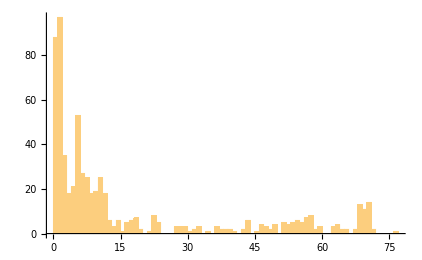

```mathematica
Histogram[lineDistance/@Flatten[flattenLines/@allLines],{1}]
```

### Optimizing Parameters

I made functions to rapidly visualize the performance of ImageLines with different settings.

```mathematica
visualizeLongLineDetect[imagesLocal[[2]],{0.02,0.04},{0.005,0.01},35]
```

| t = 0.02 | t = 0.04
d=0.005 | -Graphics- | -Graphics-
d=0.01 | -Graphics- | -Graphics-

Note that ImageLines finds light lines on a dark background.

```mathematica
With[{i=imagesLocal[[1]]},
HighlightImage[i,{Red,ImageLines[#,0.05,0.1,Method->{"Segmented"->True}]}]&/@{i,ColorNegate@i}]
```

{-Graphics-,-Graphics-}

## Pick long lines

The function ImageLines returns many spurious lines with my lenient settings, so filter out the small ones.

### Current

Take the lines above the set threshold length.

```mathematica
longLines=pickLongLines[allLines,lineSize];
showLines[i,longLines]
```

-Graphics-

### Additional Info

#### Short lines that are not used in the analysis.

```mathematica
showLines[i,Complement[Flatten[flattenLines/@allLines],longLines]]
```

-Graphics-

## Find parallel lines

In case of duplicate lines, start grouping lines in ways to simplify the merging process. Parallel lines in structure diagrams are a good way to divide the lines because for readability, parallel lines usually do not appear next to one another.

### Current

```mathematica
parallelLongLinesByAngle=Gather[Sort[longLines],Not[degreeTolerance<Abs[lineAngle[#1]/Degree-lineAngle[#2]/Degree]<(180-degreeTolerance)]&];
```

### Visualize it

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,parallelLongLinesByAngle[[n]]],ImageSize->Medium],{n,1,Length[parallelLongLinesByAngle],1},SaveDefinitions->True]
```

#### Inspect the distribution of orientations of the lines in the structure.

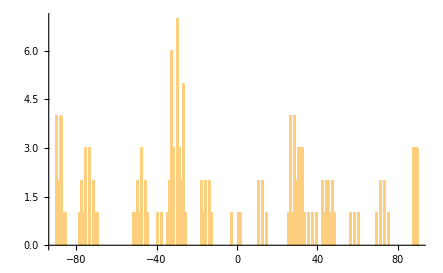

```mathematica
angles=Map[lineAngle,longLines,{1}]/Degree;
Histogram[angles,{1}]
```

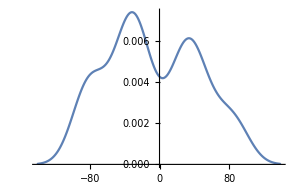

```mathematica
SmoothHistogram[angles]
```

In the future, I could group lines by these peaks or deduce something about the structure from the number of different parallel line groups.

## Nearby lines

One step closer to merging, group the lines which are nearby.

### Current

```mathematica
nearbyParallelLinesByAngle=Map[gatherNearbyLinesByCenter[#,80]&,parallelLongLinesByAngle];
```

### Visualize it

```mathematica
Manipulate[HighlightImage[i,nearbyParallelLinesByAngle[[n,m]],ImageSize->Medium],{{m,1,"Close Set"},1,10,1},{{n,1,"Parallel Set"},1,Length@nearbyParallelLinesByAngle,1},SaveDefinitions->True]
```

## Deal with intersecting lines

Finally, group intersecting lines which are parallel and nearby to mark them for merging. Intersecting lines are identified as a list containing pairs of intersecting lines.

### Current

Group the intersecting lines

```mathematica
intersectingNearbyParallelLinesByAngle=Map[gatherIntersectingLines,nearbyParallelLinesByAngle,{2}];
```

Get the single lines which are in their own lists, and set them aside.

```mathematica
singlesA=Cases[intersectingNearbyParallelLinesByAngle,{_Line},{4}];
```

Collect the other sets of intersecting lines.

```mathematica
mergeA1=Cases[intersectingNearbyParallelLinesByAngle,{{Repeated[_Line,{2}]}..},{3}];
```

```mathematica
mergeA2Prelim=Cases[intersectingNearbyParallelLinesByAngle,{Repeated[{Repeated[_Line,{2}]},{1,Infinity}],Repeated[{_Line},{1,Infinity}]},{3}];
```

```mathematica
mergeA2=DeleteCases[mergeA2Prelim,{_Line},{2}];
```

```mathematica
mergeA=Join[mergeA1,mergeA2];
```

```mathematica
mergedIntersectingNearbyParallelLinesByAngle= Map[mergeLines,mergeA,{1}];
```

```mathematica
cleanLines=Flatten@Join[singlesA,mergedIntersectingNearbyParallelLinesByAngle];
```

### Visualize it

Here are the lines marked to be merged with other lines.

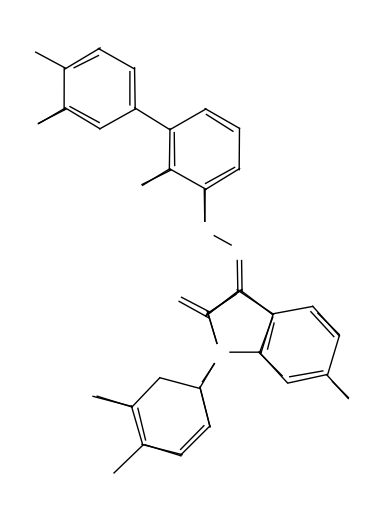

```mathematica
Graphics[cleanLines]
```

## Locate and merge vertices

To identify atom positions in the structure, I start with the vertices of all lines and join nearby ones using a radius. The radius is not yet automatically set.

### Current

```mathematica
cleanPoints=Sort@Flatten[First/@cleanLines,1];
```

```mathematica
mergedPoints=Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<mergeThreshold&]]];
```

```mathematica
cleanPointsGathered=Gather[cleanPoints,EuclideanDistance[#1,#2]<mergeThreshold&];
```

```mathematica
mergedPoints=Point/@Mean/@cleanPointsGathered;
```

### Visualize the process

```mathematica
Manipulate[Graphics[{Thin,Gray,cleanLines,Black,Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<t&]]]}],{{t,1,"Merge Threshold"},1,200},SaveDefinitions->True]
```

## Building graph edges

### Point to (vertex to vertex to) point

I use the first association to trace a given merged vertex to its parent vertices which come from the line endpoints. I then use Part expressions to extract the other point of each line and use the second association to find its merged “child”. This process builds the EdgeList necessary for any graph representation of the chemical structure.

```mathematica
mergedPointParents=AssociationThread[mergedPoints,Map[Point,cleanPointsGathered,{2}]];
```

```mathematica
separatePointsChild=Merge[Flatten@Map[Reverse,Thread/@Normal[mergedPointParents],{2}],Identity];
```

### Tracing vertices

Here I trace all central vertices...

```mathematica
edgeListTargets=Map[traceConnections[#,cleanLines,mergedPoints,mergedPointParents,separatePointsChild]&,mergedPoints];
```

...to build the edge list.

```mathematica
edgePairs=Thread/@Transpose[{Range[Length[edgeListTargets]],edgeListTargets}];
```

```mathematica
edgeList=Flatten@Map[UndirectedEdge@@#&,edgePairs,{2}];
directedEdgeList=Flatten@Map[DirectedEdge@@#&,edgePairs,{2}];
```

### Visualize it

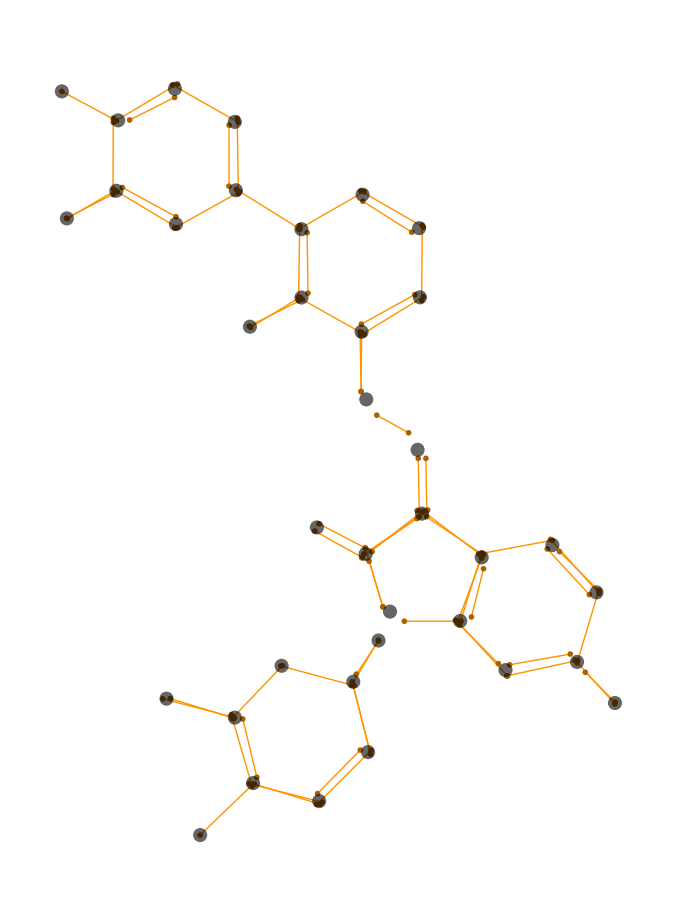

```mathematica
Graphics[{Hue[0.096],cleanLines,Darker[Hue[0.096]],Opacity[1],Directive[PointSize->0.006],Point/@cleanPoints,Opacity[0.6],Directive[PointSize->0.015],Black,mergedPoints}]
```

### Room for improvement

Currently, there is a flat cutoff, which sometimes leads the molecule to be split into disconnected subgraphs.

## Graph of molecule

### Messy Graph

The general structure of the molecule (usually) shows up in the messy graph.

```mathematica
graphOfMolecule=Graph[Range[Length[mergedPoints]],directedEdgeList];
```

```mathematica
{i,Show[graphOfMolecule]}
```

{-Graphics-,-Graphics-}

### Structure graph

To show the general layout of the molecule, remove duplicate edge pairs and self-bonds.

```mathematica
noDuplicateEdgePairs=DeleteDuplicates[Sort/@Flatten[edgePairs,1]];
```

```mathematica
noSelfBond=DeleteCases[noDuplicateEdgePairs,{ee_,ee_}];
```

```mathematica
undirectedEdgeList=Map[UndirectedEdge@@#&,noSelfBond,{1}];
```

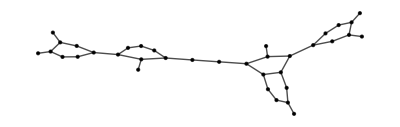

```mathematica
Graph[Range[Length[mergedPoints]],undirectedEdgeList,EdgeStyle->Black,VertexStyle->Black]
```

### Next step

The function Molecule requires an atom list and bond list.

```mathematica
Molecule[{"N","C","Br","Cl","C"},{Bond[{1,2},"Single"],Bond[{2,3},"Single"],Bond[{2,4},"Single"],Bond[{2,5},"Single"]}]
```

Molecule[…]

Identification of atoms is not complete, so for now we can assume all labeled atoms are carbon.

```mathematica
atomList=Table["C",Length[mergedPoints]];
```

Create the proper bond data structure by

```mathematica
bondList=Apply[Bond@*List,noSelfBond,2];
```

```mathematica
Molecule[atomList,bondList]
```

Molecule[…]

## Data Structure

## Future Work

There remain a few steps (outlined for now)

## Atom recognition and assignment

The main aspect to complete is to associate labels on the structure with the appropriate vertices. There are a few ways of doing this.

### Image Segmentation

The functions MorphologicalComponents combined with ComponentMeasurements enable feature extraction:

```mathematica
With[{i=imagesLocal[[2]]},
components=MorphologicalComponents@ColorNegate@i;
extractedInfo=ComponentMeasurements[{components,ColorNegate@i},{"MaskedImage","BoundingBox"},All,"Dataset"];
Colorize[components,ImageSize->Medium]]
```

-Graphics-

Features can be extracted, and TextRecognize works quite well on the text elements.

```mathematica
symbols=ColorNegate/@Association@Normal@extractedInfo[All,"MaskedImage"];
recognizedSymbol=TextRecognize[ImagePad[#,100,1],RecognitionPrior->"Character"]&/@symbols;
Merge[{symbols,recognizedSymbol}, Identity]//Dataset
```

Dataset[<>]

There are many properties available to help screen out the large segments of the image.

```mathematica
props=ComponentMeasurements[{components,ColorNegate@i},"Properties"]
```

{AdjacentBorderCount,AdjacentBorders,Area,AreaRadiusCoverage,AuthalicRadius,BoundingBox,BoundingBoxArea,BoundingDiskCenter,BoundingDiskCoverage,BoundingDiskRadius,CaliperElongation,CaliperLength,CaliperWidth,Centroid,Circularity,Complexity,ContourHierarchy,Contours,ConvexArea,ConvexCount,ConvexCoverage,ConvexPerimeterLength,ConvexVertices,Count,Data,DenseContours,Dimensions,Eccentricity,Elongation,EmbeddedComponentCount,EmbeddedComponents,EnclosingComponentCount,EnclosingComponents,Energy,Entropy,EquivalentDiskRadius,EulerNumber,ExteriorNeighborCount,ExteriorNeighbors,FilledCircularity,FilledCount,Fragmentation,Holes,Image,IntensityCentroid,IntensityData,InteriorNeighborCount,InteriorNeighbors,Label,LabelCount,Length,Mask,MaskedImage,Max,MaxCentroidDistance,MaxIntensity,MaxPerimeterDistance,Mean,MeanCaliperDiameter,MeanCentroidDistance,MeanIntensity,Median,MedianIntensity,Medoid,Min,MinCentroidDistance,MinimalBoundingBox,MinIntensity,NeighborCount,Neighbors,Orientation,OuterPerimeterCount,PerimeterCount,PerimeterLength,PerimeterPositions,PolygonalLength,Rectangularity,SemiAxes,Skew,StandardDeviation,StandardDeviationIntensity,Total,TotalIntensity,Width}

#### Concept

One simple idea is to remove an image segment whose bounding box includes both endpoints of a line to effectively screen out lines.

### Recognize text

Visualize the capabilities of TextRecognize on generic regions. Mouse over to see the recognized text in the region highlighted.

```mathematica
a={100,100};b={200,200};
Manipulate[
LocatorPane[Dynamic[{a,b},
{
({a,b}=#)&
,(text=TextRecognize[imagesLocal[[i]],Masking->Apply[Rectangle,#],RecognitionPrior->r])&
}
],
Dynamic[
HighlightImage[imagesLocal[[i]],Tooltip[Rectangle[a,b],text],ImageSize->Medium]
]
,{{1,1},ImageDimensions[imagesLocal[[i]]],{1,1}}
]
,{i,1,Length[imagesLocal],1},{r,{"SparseText","Character","Word","Line","Block"}}]
```

## Other Tests

## Image processing

### Edge Detection

```mathematica
Manipulate[EdgeDetect[Dilation[ColorNegate@i,1],r,t,Method->{m,"StraightEdges"->s}],{{r,1},0.5,10},{{t,0.5},0,1},{m,{"Canny","ShenCastan","Sobel"}},{s,0,1},SaveDefinitions->True]
```